```mathematica
T[r_,rs_,tp_,pl_]:=(Sqrt[(r-rs)^2]-pl)/tp
q[r_,rs_]:=2 T[r,rs]^3-3 T[r,rs]^2+1
```

```mathematica
Q[r_,rs_,tp_,pl_]:=Piecewise[{{1, Abs[r-rs]≤pl}, {2 T[r,rs,tp,pl]^3-3 T[r,rs,tp,pl]^2+1, tp<Abs[r-rs]<pl+tp}, {0, Abs[r-rs]≥pl+tp}}]
```

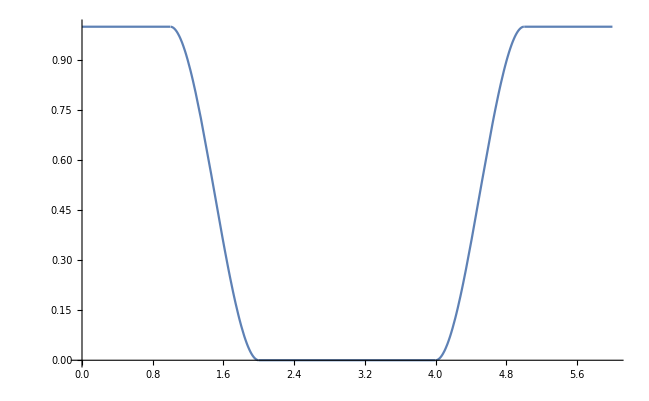

```mathematica
Plot[1-Q[r,3,1,1],{r,0,6}]
```

```mathematica
Fs[t_,r_]:=1/r[t]
```

```mathematica
D[Fs[t,r],r[t]]
```

-1/r[t]^2

```mathematica
D[Q[r,rs,tp,pl],r]
```

Piecewise[{{0, pl-Abs[r-rs]≥0}, {(6 (-pl+√((r-rs)^2))^2 (r-rs))/(√((r-rs)^2) tp^3)-(6 (-pl+√((r-rs)^2)) (r-rs))/(√((r-rs)^2) tp^2), tp-Abs[r-rs]<0&&pl+tp-Abs[r-rs]>0}, {0, True}}]

```mathematica
D[2 T[r,rs,tp,pl]^3-3 T[r,rs,tp,pl]^2+1,r]
```

(6 (-pl+√((r-rs)^2))^2 (r-rs))/(√((r-rs)^2) tp^3)-(6 (-pl+√((r-rs)^2)) (r-rs))/(√((r-rs)^2) tp^2)

```mathematica
DiW[r_,rs_,tp_,pl_]:=Piecewise[{{0, pl-Abs[r-rs]≥0}, {(6 (-pl+√((r-rs)^2))^2 (r-rs))/(√((r-rs)^2) tp^3)-(6 (-pl+√((r-rs)^2)) (r-rs))/(√((r-rs)^2) tp^2), tp-Abs[r-rs]<0&&pl+tp-Abs[r-rs]>0}, {0, True}}]
```

```mathematica
rs=1;
```

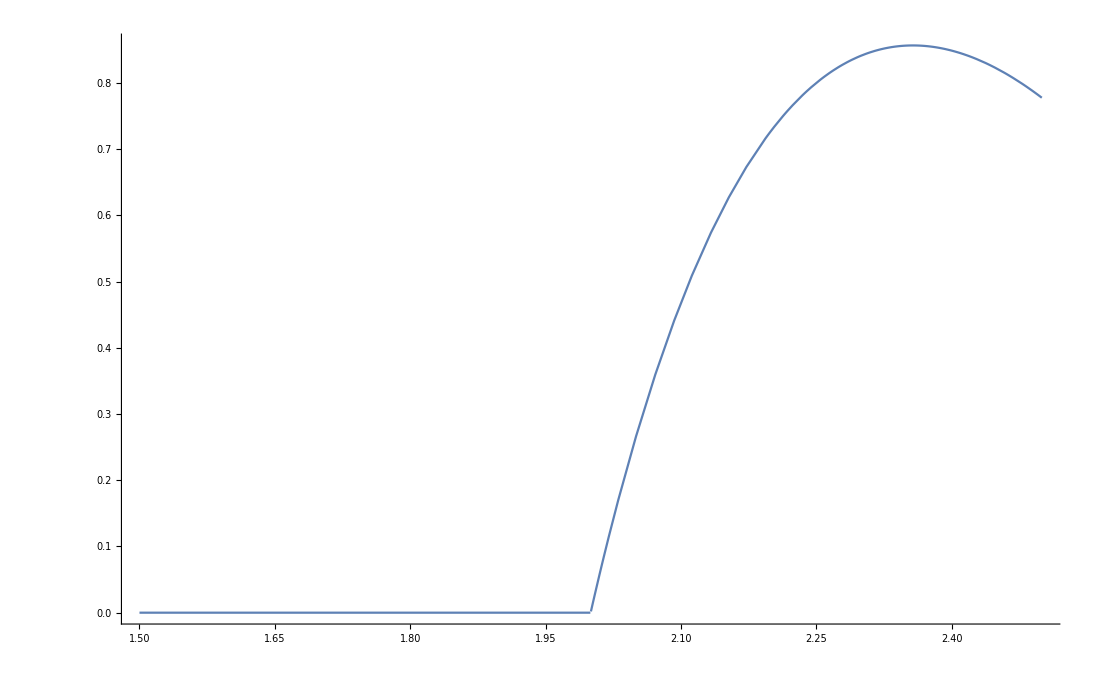

```mathematica
Plot[(-DiW[r,rs,1,1])/(r-rs)-(1-Q[r,rs,1,1])/(r-rs)^2,{r,1.5,2.5},PlotRange->All]
```

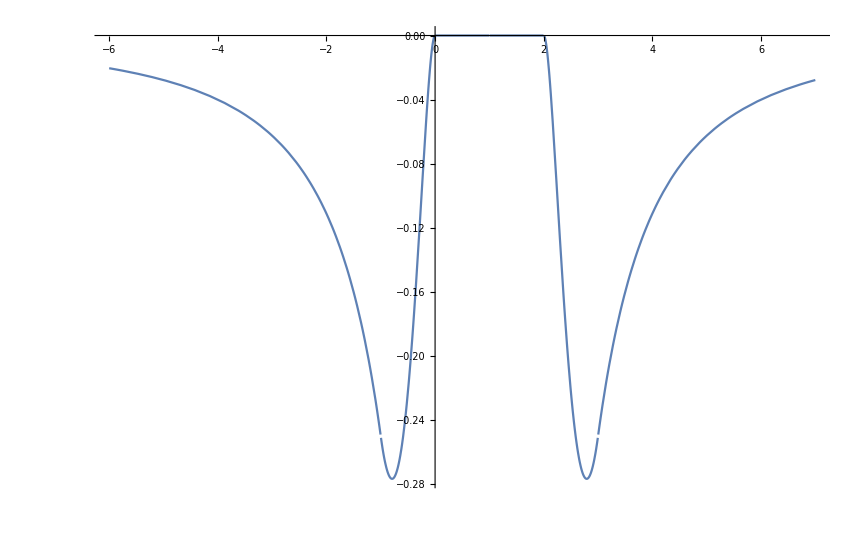

```mathematica
Plot[-(1-Q[r,rs,1,1])/(r-rs)^2,{r,-6,7},PlotRange->All]
```